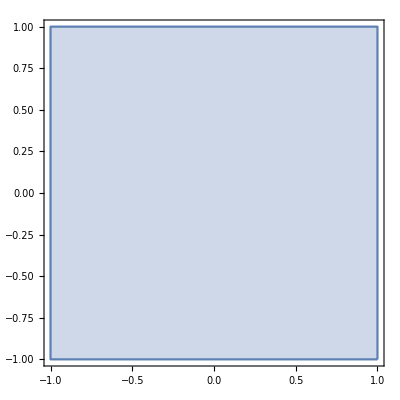

```mathematica
Ω0=Rectangle[{-1,-1},{1,1}];
RegionPlot[Ω0]
```

```mathematica
sol0=NDSolveValue[{∇_{x,y}^2 u[x,y]==NeumannValue[-1.,x≤-1]+NeumannValue[+1,x≥1],DirichletCondition[u[x,y]==0,x==-1]},u,{x,y}∈Ω0];
```

```mathematica
Plot3D[sol0[x,y],{x,y}∈Ω0,,PlotRange->All]
```

-Graphics3D-